```mathematica
Dsolve[(1-x^2 )y''[x]- 2xy'[x]+n(n+1)y[x]==0, y[x],x]
```

Dsolve[n (1+n) y[x]-2 xy'[x]+(1-x^2) y''[x]==0,y[x],x]

```mathematica
Table[{n,LegendreP[n,x]},{n, 0, 6}]
```

{{0,1},{1,x},{2,1/2 (-1+3 x^2)},{3,1/2 (-3 x+5 x^3)},{4,1/8 (3-30 x^2+35 x^4)},{5,1/8 (15 x-70 x^3+63 x^5)},{6,1/16 (-5+105 x^2-315 x^4+231 x^6)}}

```mathematica
leg0to6=Table[LegendreP[n,x],{n,0,6}]
```

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4),1/8 (15 x-70 x^3+63 x^5),1/16 (-5+105 x^2-315 x^4+231 x^6)}

```mathematica
Plot[LegendreP[n,x], {n,6}, {x, -1,1}]
```

Plot::nonopt: Options expected (instead of {x,-1,1}) beyond position 2 in Plot[LegendreP[n,x],{n,6},{x,-1,1}]. An option must be a rule or a list of rules.

```mathematica
Plot[LegendreP[n,x],{n,6},{x,-1,1}]
```

Plot::nonopt: Options expected (instead of {x,-1,1}) beyond position 2 in Plot[LegendreP[n,x],{n,6},{x,-1,1}]. An option must be a rule or a list of rules.

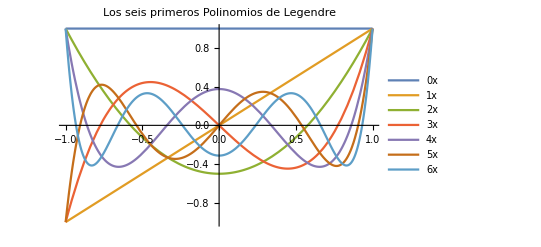

```mathematica
Plot[{LegendreP[0,x], LegendreP[1,x], LegendreP[2,x], LegendreP[3,x], LegendreP[4,x], LegendreP[5,x], LegendreP[6,x]},{x,-1,1}, PlotLegends->"Expressions", PlotLabel->"Los seis primeros Polinomios de Legendre"]
```

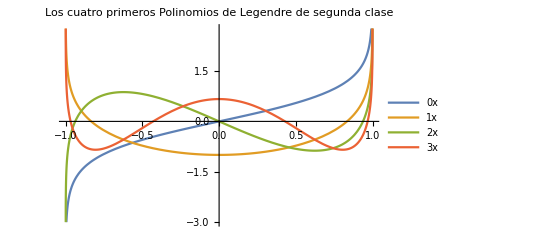

```mathematica
Plot[{LegendreQ[0,x], LegendreQ[1,x], LegendreQ[2,x], LegendreQ[3,x]},{x,-1,1}, PlotLegends->"Expressions", PlotLabel->"Los cuatro primeros Polinomios de Legendre de segunda clase"]
```